```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.100(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

```mathematica
(*pp100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100b.csv"];*)
```

```mathematica
pp100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100b.csv"];
```

```mathematica
pp100a=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+I*pp100a[[All,3]]}];
pp100b=Transpose[{pp100b[[All,1]],pp100b[[All,2]]+I*pp100b[[All,3]]}];
```

```mathematica
θpp100=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+pp100b[[All,2]]}];
```

```mathematica
θtoq[x_]:={2 Sqrt[En^2+2*En*m] Sin[x[[1]] Pi/360],x[[2]]}
```

```mathematica
pp100=θtoq/@θpp100;
```

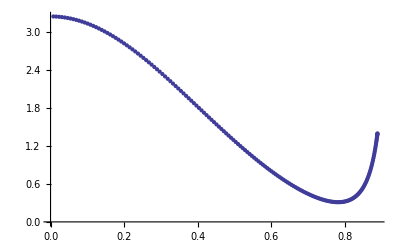

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Re[pp100[[All,2]]]}]]
```

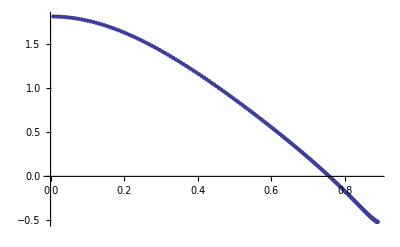

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Im[pp100[[All,2]]]}]]
```

```mathematica
f=Interpolation[pp100];
```

InterpolatingFunction::dmval: Input value {0.0000181644} lies outside the range of data in the interpolating function. Extrapolation will be used.

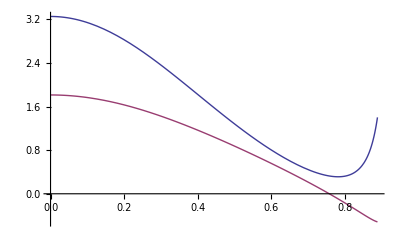

```mathematica
Plot[{Re[f[q]],Im[f[q]]},{q,0,2 P}]
```

```mathematica
Γtemp[b_]:=I/κ NIntegrate[BesselJ[0,b q] f[q] q,{q,0,2 P}]
Γprimetemp[b_]:=-I/κ NIntegrate[BesselJ[1,b q] q^2 f[q],{q,0,2 P}]
```

```mathematica
Γtab=Table[{b,Γtemp[b]},{b,0,50}];
Γ=Interpolation[Γtab];
```

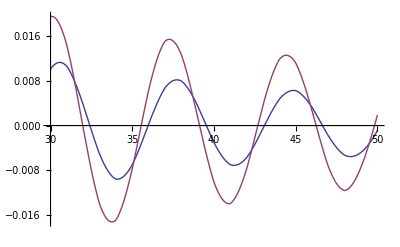

```mathematica
Plot[{Re[Γ[b]],Im[Γ[b]]},{b,30,50}]
```

```mathematica
Γprimetab=Table[{b,Γprimetemp[b]},{b,0,50}];
Γprime=Interpolation[Γprimetab];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

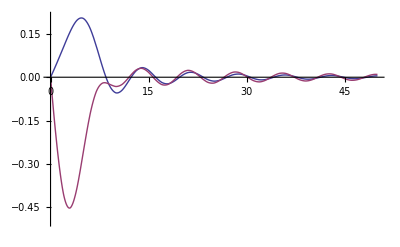

```mathematica
Plot[{Re[Γprime[b]],Im[Γprime[b]]},{b,0,50},PlotRange->{-.5,.21}]
```

```mathematica
Utemp[r_]:=I/Pi NIntegrate[(Γprime[Sqrt[r^2+u^2]]/(1-Γ[Sqrt[r^2+u^2]]) 1/Sqrt[r^2+u^2]),{u,0,Sqrt[50^2-r^2]}]
```

```mathematica
U=Quiet[Interpolation[Table[{r,Utemp[r]},{r,0,50}]]];
```

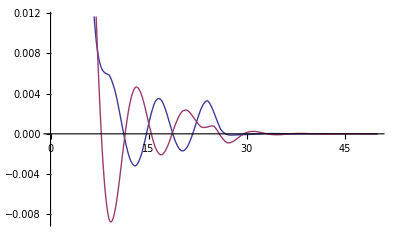

```mathematica
Plot[{Re[U[t]],Im[U[t]]},{t,0,50}]
```

```mathematica
((mp+M)/(4 Pi Sqrt[s])) NIntegrate[Exp
```

```mathematica
func[q_]:=2 I Pi NIntegrate[b BesselJ[0,q b] Log[1-Γ[b]],{b,0,50}];
```

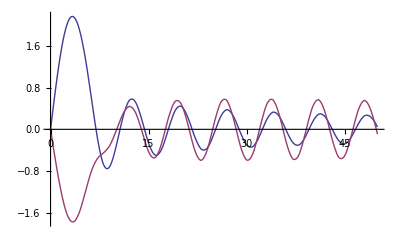

```mathematica
Plot[{Re[b BesselJ[0,0] Log[1-Γ[b]]],Im[b BesselJ[0,0] Log[1-Γ[b]]]},{b,0,50}]
```

```mathematica
func[3]
```

-15.9903-30.5954 ⅈ